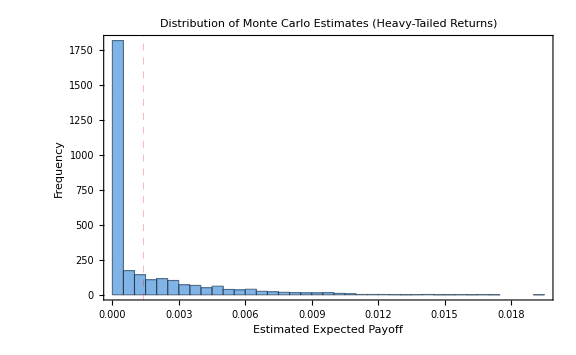

crash prob (put ITM)      : 1.23×10^-4 (~0.6 crashes per run)

TRUE E[payoff] (quad)     : 0.00141

crude MC  mean of estimates: 0.00144   <- ~unbiased in expectation

crude MC  MEDIAN estimate  : 0.00000   <- the TYPICAL run

std of estimates : 0.00253

coeff of variation: 1.75

frac of runs < 50% of true : 633/10%

frac of runs that saw 0    : 160/3%

five individual affordable runs: {0.0025,0.0008,0.0000,0.0000,0.0000}

```mathematica
(*Part one*)
(*Log return, assuming a fat tailed distribution*)
(*Ensure reproducibility*)
SeedRandom[0];
s0=100.0;
nu=3.0;
sigma=0.05;
tScale=sigma/Sqrt[nu/(nu-2.0)];
mu=0.0;
(*Define the return distribution*)
dist=StudentTDistribution[mu,tScale,nu];
(*----Hedge:deep OTM put,only pays in a crash----*)
k=55.0;
putPayoff[r_]:=Max[k-s0*Exp[r],0.0];
(*----Ground truth via numerical integration----*)
trueVal=NIntegrate[putPayoff[r]*PDF[dist,r],{r,-6.0,6.0},Method->"LocalAdaptive"];
rStar=Log[k/s0];
pCrash=CDF[dist,rStar];
(*----Crude MC at an affordable N,compiled for speed----*)
nAfford=5000;
trials=3000;
(*Compile the sampling and expectation loop for speed*)
mcTrials=Compile[{{n,_Integer},{numTrials,_Integer},{scale,_Real},{degFree,_Real}},Table[Mean[Map[Max[55.0-100.0*Exp[#],0.0]&,RandomVariate[StudentTDistribution[0.0,scale,degFree],n]]],{numTrials}],RuntimeOptions->"Speed"][nAfford,trials,tScale,nu];
(*Visualize*)
Histogram[mcTrials,50,"Count",ChartStyle->Directive[RGBColor[0.5,0.7,0.9],EdgeForm[Black]],GridLines->{{{trueVal,Directive[Red,Thick,Dashed]},{medianEst,Directive[DarkGreen,Thick,Dotted]}},None},PlotLabel->"Distribution of Monte Carlo Estimates (Heavy-Tailed Returns)",FrameLabel->{"Estimated Expected Payoff","Frequency"},Frame->True,ImageSize->Large,PlotRange->All]
(*----Compute statistics----*)
meanEst=Mean[mcTrials];
medianEst=Median[mcTrials];
stdEst=StandardDeviation[mcTrials];
cvEst=stdEst/meanEst;
fracUnderHalf=Count[mcTrials,x_/;x<0.5*trueVal]/trials;
fracZero=Count[mcTrials,0.0]/trials;

(*Sample 5 individual runs*)
fiveRuns=Table[Mean[Max[k-s0*Exp[#],0.0]&/@RandomVariate[dist,nAfford]],{5}];

(*----Print Results----*)
Print[StringForm["crash prob (put ITM)      : `` (~`` crashes per run)",ScientificForm[pCrash,3],NumberForm[nAfford*pCrash,{4,1}]]];
Print[StringForm["TRUE E[payoff] (quad)     : ``",NumberForm[trueVal,{6,5}]]];
Print[StringForm["crude MC  mean of estimates: ``   <- ~unbiased in expectation",NumberForm[meanEst,{6,5}]]];
Print[StringForm["crude MC  MEDIAN estimate  : ``   <- the TYPICAL run",NumberForm[medianEst,{6,5}]]];
Print[StringForm["          std of estimates : ``",NumberForm[stdEst,{6,5}]]];
Print[StringForm["          coeff of variation: ``",NumberForm[cvEst,{3,2}]]];
Print[StringForm["frac of runs < 50% of true : ``%",NumberForm[fracUnderHalf*100,{4,2}]]];
Print[StringForm["frac of runs that saw 0    : ``%",NumberForm[fracZero*100,{4,2}]]];
Print["five individual affordable runs: ",Map[ToString[NumberForm[#,{5,4}]]&,fiveRuns]];
```